```mathematica
Integrate[2 v0/Sqrt[4 v0-1-(4 v0-2) x^2-x^4],{x,-1,0},v0∈Reals]
```

2 v0 (v0∈Reals) If[(4 v0+Abs[1-4 v0]≠1&&(√(1-4 v0)∉Reals||v0∉Reals||4 Re[v0]≥1))||Re[√(1-4 v0)]≥1,(√(v0/(-1+4 v0)) EllipticK[1/(1-4 v0)])/(√v0),Integrate[1/(√(1-x^2) √(-1+4 v0+x^2)),{x,-1,0},Assumptions→0<v0≤1/4||(v0∈Reals&&0<Re[v0]<1/4)]]

```mathematica
f[v0_]:=Integrate[2 v0/Sqrt[4 v0-1-(4 v0-2) x^2-x^4],{x,-1,0}];
```

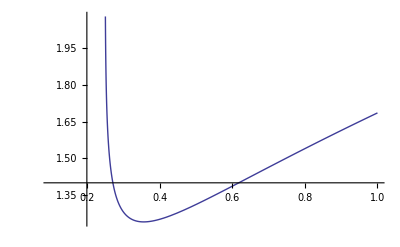

```mathematica
Plot[f[y],{y,0.1,1}]
```

```mathematica
N[f[1/5],100]
```

0.9028821307283414620333024018093549588941677126959997972621591916208778478162328360357388530760338782-0.663849439444211200340499063694312606959264220831669930918189353318214323059576691647270033140939002 ⅈ

```mathematica
NSolve[f[x]==1.4,x]
```

Solve::dinv: The expression ∫_-1 0 2 x/√-1 + 4 x - x^4 - x^2 (-2 + 4 x) ⅆ x involves unknowns in more than one argument, so inverse functions cannot be used.

NSolve[∫_-1^0 (2 x)/(√(-1+4 x-x^4-x^2 (-2+4 x)))ⅆx==1.4,x]